```mathematica
SetDirectory["FileName"/.NotebookInformation[EvaluationNotebook[]]/.FrontEnd`FileName[d_List,nam_,___]:>ToFileName[d]];
```

## Initial phase - W0-W40

### DATA - R0

```mathematica
sample=Transpose[ToExpression[Import["samplep15.xlsx"][[1]]]];
```

```mathematica
parameters={
{beta,0.7*0.5,1.15*0.5},
{phi,0.85*1.65,1.5*1.65},
{theta,0.25*0.4,1.2*0.4},
{gamma,0.95*0.7,1.05*0.7},
{delta,0.69,0.73},
{gammaT,0.95*1.5,1.05*1.5},
{deltaT,0.52,0.64},
{eta,0.95*1.4,1.05*1.4},
{b,0.9*1.17,1.5*1.17},
{kappa,0.9*0.0025,1.1*0.0025},
{alpha,0.95*0.7,1.05*0.7},
{EE0,0,15*10^-6},
{II0,0,15*10^-6},
{DD0,0,15*10^-6},
{HH0,0,15*10^-6}}
```

{{beta,0.35,0.575},{phi,1.4025,2.475},{theta,0.1,0.48},{gamma,0.665,0.735},{delta,0.69,0.73},{gammaT,1.425,1.575},{deltaT,0.52,0.64},{eta,1.33,1.47},{b,1.053,1.755},{kappa,0.00225,0.00275},{alpha,0.665,0.735},{EE0,0,3/200000},{II0,0,3/200000},{DD0,0,3/200000},{HH0,0,3/200000}}

```mathematica
sampleparam=Table[Table[N[(parameters[[All,2;;3]][[j,2]]-parameters[[All,2;;3]][[j,1]])sample[[i,j]]+parameters[[All,2;;3]][[j,1]]],{j,1,Length[sample[[i]]]}],{i,1,Length[sample]}];
```

```mathematica
R0=(η θ)/(γT η+γ(γT+κ))+(β1(γT+κ))/(γT η+γ(γT+κ))+(φ(γT δT η+γ δ(γT+κ)))/(b(γT η+γ(γT+κ)))
```

(η θ)/(γT η+γ (γT+κ))+(β1 (γT+κ))/(γT η+γ (γT+κ))+((γT δT η+γ δ (γT+κ)) φ)/(b (γT η+γ (γT+κ)))

```mathematica
R0C=(β1(γT+κ))/(γT η+γ(γT+κ));
R0H=(η θ)/(γT η+γ(γT+κ));
R0F=(φ(γT δT η+γ δ(γT+κ)))/(b(γT η+γ(γT+κ)));
```

```mathematica
R0s=Table[R0/.{β1->sampleparam[[i,1]],φ->sampleparam[[i,2]],θ->sampleparam[[i,3]],γ->sampleparam[[i,4]],δ->sampleparam[[i,5]],γT->sampleparam[[i,6]],δT->sampleparam[[i,7]],η->sampleparam[[i,8]],b->sampleparam[[i,9]],κ->sampleparam[[i,10]]},{i,1,Length[sample]}];
R0Cs=Table[R0C/.{β1->sampleparam[[i,1]],φ->sampleparam[[i,2]],θ->sampleparam[[i,3]],γ->sampleparam[[i,4]],δ->sampleparam[[i,5]],γT->sampleparam[[i,6]],δT->sampleparam[[i,7]],η->sampleparam[[i,8]],b->sampleparam[[i,9]],κ->sampleparam[[i,10]]},{i,1,Length[sample]}];
R0Hs=Table[R0H/.{β1->sampleparam[[i,1]],φ->sampleparam[[i,2]],θ->sampleparam[[i,3]],γ->sampleparam[[i,4]],δ->sampleparam[[i,5]],γT->sampleparam[[i,6]],δT->sampleparam[[i,7]],η->sampleparam[[i,8]],b->sampleparam[[i,9]],κ->sampleparam[[i,10]]},{i,1,Length[sample]}];
R0Fs=Table[R0F/.{β1->sampleparam[[i,1]],φ->sampleparam[[i,2]],θ->sampleparam[[i,3]],γ->sampleparam[[i,4]],δ->sampleparam[[i,5]],γT->sampleparam[[i,6]],δT->sampleparam[[i,7]],η->sampleparam[[i,8]],b->sampleparam[[i,9]],κ->sampleparam[[i,10]]},{i,1,Length[sample]}];
```

```mathematica
{Min[R0s],Max[R0s]}
```

{0.751728,1.91894}

```mathematica
{Min[R0Cs],Max[R0Cs]}
```

{0.160151,0.286123}

```mathematica
{Min[R0Hs],Max[R0Hs]}
```

{0.0418779,0.226586}

```mathematica
{Min[R0Fs],Max[R0Fs]}
```

{0.480877,1.4924}

```mathematica
joint=Join[{Join[parameters[[1;;10,1]],{"R0"}]},Table[Join[sampleparam[[i]][[1;;10]],{R0s[[i]]}],{i,1,Length[sampleparam]}]]
```

{{beta,phi,theta,gamma,delta,gammaT,deltaT,eta,b,kappa,R0},{0.574868,1.86525,0.121942,0.679391,0.694049,1.54428,0.626377,1.37333,1.38138,0.00267891,1.20924},9998,{0.461106,1.50507,0.18815,0.733244,0.724999,1.46811,0.565491,1.39323,1.5681,0.00265228,0.896622}}
 |  |  |  |

```mathematica
Export["R0tp10.csv",joint]
```

R0tp10.csv

### DATA+FITTING - Fitting with LSM

```mathematica
ode[{β1_?NumberQ,φ1_?NumberQ,θ1_?NumberQ,γ1_?NumberQ,δ1_?NumberQ,γH1_?NumberQ,δH1_?NumberQ,η1_?NumberQ,b1_?NumberQ,κ1_?NumberQ,α1_?NumberQ},{S0_?NumberQ,EE0_?NumberQ,II0_?NumberQ,RR0_?NumberQ,DD0_?NumberQ,BB0_?NumberQ,HH0_?NumberQ}]:=(odenew[{β1,φ1,θ1,γ1,δ1,γH1,δH1,η1,b1,κ1,α1},{S0,EE0,II0,RR0,DD0,BB0,HH0}]=NDSolveValue[
{S'[t]==-β1/22 S[t]II[t]-φ1/22 S[t]DD[t]-θ1/22 S[t]HH[t],
EE'[t]==β1/22 S[t]II[t]+φ1/22 S[t]DD[t]+θ1/22 S[t]HH[t]-α1 EE[t],
II'[t]==α1 EE[t]-γ1 II[t]-η1 II[t]+κ1 HH[t],
RR'[t]==(1-δ1)γ1 II[t]+(1-δH1)γH1 HH[t],
DD'[t]==δ1 γ1 II[t]-b1 DD[t]+δH1 γH1 HH[t],
BB'[t]==b1 DD[t],
HH'[t]==η1 II[t]-γH1 HH[t]-κ1 HH[t],
S[0]==S0,EE[0]==EE0,II[0]==II0,RR[0]==RR0,DD[0]==DD0,BB[0]==BB0,HH[0]==HH0},{S[t],EE[t],II[t],RR[t],DD[t],BB[t],HH[t]},{t,0,50}])
```

```mathematica
samplesol=Table[ode[sampleparam[[i,1;;11]],{22,sampleparam[[i,12]],sampleparam[[i,13]],0,sampleparam[[i,14]],0,sampleparam[[i,15]]}],{i,1,Length[sampleparam]}];
```

```mathematica
samplepoints=Table[sampleparam[[i,11]]Evaluate[samplesol[[i]][[2]]/.{t->j}],{i,1,Length[sampleparam]},{j,1,40,1}];
```

```mathematica
data=ToExpression[Import["ebola.xlsx"]][[1]];
```

```mathematica
guineaweekly=Table[{data[[i,1]],data[[i,2]]},{i,2,Length[data]}];
```

```mathematica
liberiaweekly=Table[{data[[i,1]],data[[i,3]]},{i,2,Length[data]}];
```

```mathematica
sieraleoneweekly=Table[{data[[i,1]],data[[i,4]]},{i,2,Length[data]}];
```

```mathematica
totalcasesweekly=Table[guineaweekly[[i,2]]+liberiaweekly[[i,2]]+sieraleoneweekly[[i,2]],{i,1,Length[data]-1}]
```

{3.,7.,12.,16.,26.,28.,35.,42.,48.,53.,58.,117.,141.,189.,242.,265.,273.,283.,295.,295.,376.,460.,475.,575.,607.,780.,892.,1051.,1201.,1437.,1766.,2115.,2599.,3052.,3685.,4784.,5637.,6553.,7470.,8376.,9191.,10114.,13779.,13863.,14383.,15319.,15901.,17195.,17986.,18602.,19810.,20478.,20972.,21261.,21689.,22057.,22460.,22859.,23218.}

```mathematica
newinfectedweekly=Join[{totalcasesweekly[[1]]},Table[totalcasesweekly[[i]]-totalcasesweekly[[i-1]],{i,2,Length[totalcasesweekly]}]]
```

{3.,4.,5.,4.,10.,2.,7.,7.,6.,5.,5.,59.,24.,48.,53.,23.,8.,10.,12.,0.,81.,84.,15.,100.,32.,173.,112.,159.,150.,236.,329.,349.,484.,453.,633.,1099.,853.,916.,917.,906.,815.,923.,3665.,84.,520.,936.,582.,1294.,791.,616.,1208.,668.,494.,289.,428.,368.,403.,399.,359.}

```mathematica
LSlist=Table[{j,Sum[(newinfectedweekly[[i]]/1000000-samplepoints[[j,i]])^2,{i,1,Length[samplepoints[[j]]]}]},{j,1,Length[samplepoints]}];
```

```mathematica
sortedLS=SortBy[LSlist,Last];
```

```mathematica
sortedLS[[1]]
```

{783,3.36721×10^-7}

```mathematica
sortedindices=sortedLS[[All,1]];
```

```mathematica
sortedindices[[1]]
```

783

```mathematica
R0s[[sortedindices[[1]]]]
```

1.44583

```mathematica
R0Cs[[sortedindices[[1]]]]
```

0.250573

```mathematica
R0Hs[[sortedindices[[1]]]]
```

0.146585

```mathematica
R0Fs[[sortedindices[[1]]]]
```

1.04867

```mathematica
Thread[{parameters[[All,1]],sampleparam[[sortedindices[[1]]]]}]
```

{{beta,0.531912},{phi,2.10387},{theta,0.327954},{gamma,0.67078},{delta,0.728201},{gammaT,1.53033},{deltaT,0.61407},{eta,1.45437},{b,1.30432},{kappa,0.00250229},{alpha,0.694527},{EE0,3.4222×10^-6},{II0,2.31715×10^-6},{DD0,4.25041×10^-6},{HH0,1.0931×10^-7}}

### PLOT+FITTING - Confidence bands

```mathematica
{beta0,phi0,theta0,gamma0,delta0,gammaT0,deltaT0,eta0,b0,kappa0,alpha0,E0,I0,D0,H0}=sampleparam[[sortedindices[[1]]]]
```

{0.531912,2.10387,0.327954,0.67078,0.728201,1.53033,0.61407,1.45437,1.30432,0.00250229,0.694527,3.4222×10^-6,2.31715×10^-6,4.25041×10^-6,1.0931×10^-7}

```mathematica
parameterscb={
{beta,0.95*beta0,1.05*beta0},
{phi,0.95*phi0,1.05*phi0},
{theta,0.95*theta0,1.05*theta0},
{gamma,0.95*gamma0,1.05*gamma0},
{delta,0.95*delta0,1.05*delta0},
{gammaT,0.95*gammaT0,1.05*gammaT0},
{deltaT,0.95*deltaT0,1.05*deltaT0},
{eta,0.95*eta0,1.05*eta0},
{b,0.95*b0,1.05*b0},
{kappa,0.95*kappa0,1.05*kappa0},
{alpha,0.95*alpha0,1.05*alpha0},
{EE0,0.95*E0,1.05*E0},
{II0,0.95*I0,1.05*I0},
{DD0,0.95*D0,1.05*D0},
{HH0,0.95*H0,1.05*H0}
}
```

{{beta,0.505316,0.558508},{phi,1.99868,2.20907},{theta,0.311556,0.344352},{gamma,0.637241,0.704319},{delta,0.691791,0.764611},{gammaT,1.45381,1.60684},{deltaT,0.583367,0.644774},{eta,1.38166,1.52709},{b,1.2391,1.36953},{kappa,0.00237717,0.0026274},{alpha,0.6598,0.729253},{EE0,3.25109×10^-6,3.59331×10^-6},{II0,2.20129×10^-6,2.433×10^-6},{DD0,4.03789×10^-6,4.46293×10^-6},{HH0,1.03844×10^-7,1.14775×10^-7}}

```mathematica
sampleparamcb=Table[Table[N[(parameterscb[[All,2;;3]][[j,2]]-parameterscb[[All,2;;3]][[j,1]])sample[[i,j]]+parameterscb[[All,2;;3]][[j,1]]],{j,1,Length[sample[[i]]]}],{i,1,Length[sample]}]
```

{{0.558476,2.08945,0.31345,0.651031,0.699162,1.5755,0.637802,1.42667,1.30011,0.00259182,0.701415,3.38329×10^-6,2.23976×10^-6,4.31055×10^-6,1.1185×10^-7},9998,{0.531582,2.0188,0.319164,0.702636,0.755506,5,0.700423,3.4817×10^-6,2.24603×10^-6,4.05354×10^-6,1.10536×10^-7}}
 |  |  |  |

```mathematica
samplesolcb=Table[ode[sampleparamcb[[i,1;;11]],{22,sampleparamcb[[i,12]],sampleparamcb[[i,13]],0,sampleparamcb[[i,14]],0,sampleparamcb[[i,15]]}],{i,1,Length[sampleparamcb]}];
```

```mathematica
samplepointscb=Table[sampleparamcb[[i,12]]+sampleparamcb[[i,11]]NIntegrate[Evaluate[samplesolcb[[i]][[2]]/.{t->s}],{s,0,j}],{i,1,Length[sampleparamcb]},{j,1,40,1}];
```

```mathematica
LSlistcb=Table[{j,Sum[(totalcasesweekly[[i]]/1000000-samplepointscb[[j,i]])^2,{i,1,Length[samplepointscb[[j]]]}]},{j,1,Length[samplepointscb]}];
```

```mathematica
sortedLScb=SortBy[LSlistcb,Last];
```

```mathematica
sortedLScb[[1]]
```

{1919,2.75704×10^-6}

```mathematica
sortedindicescb=sortedLScb[[All,1]];
```

```mathematica
sortedindicescb[[1]]
```

1919

```mathematica
complementedcb=Complement[samplepointscb,samplepointscb[[sortedindicescb[[95/100*Length[samplepointscb]+1;;Length[samplepointscb]]]]]];
```

```mathematica
lowerboundcb=Table[Min[complementedcb[[All,i]]],{i,1,40}];
```

```mathematica
upperboundcb=Table[Max[complementedcb[[All,i]]],{i,1,40}];
```

```mathematica
lowerbondcb=Interpolation[lowerboundcb];
```

```mathematica
upperbondcb=Interpolation[upperboundcb]
```

InterpolatingFunction[{{1., 40.}}, <>]

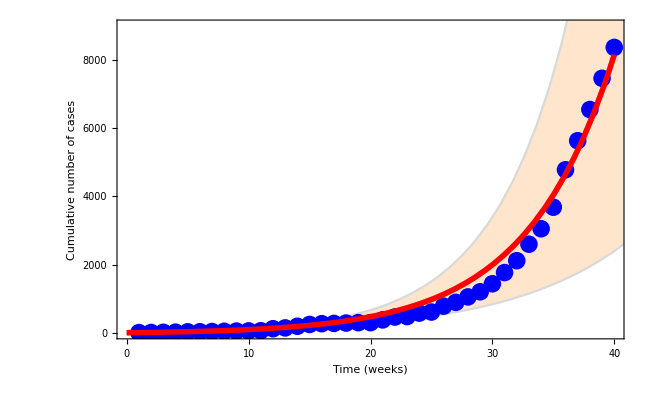

```mathematica
grconfbase=Show[Plot[1000000(sampleparam[[sortedindices[[1]],12]]+sampleparam[[sortedindices[[1]],11]]NIntegrate[Evaluate[samplesol[[sortedindices[[1]]]][[2]]/.{t->s}],{s,0,x}]),{x,0,40},Frame->True,PlotStyle->Directive[Red,Thickness[0.006]],FrameLabel->{Style["Time (weeks)",FontSize->20],Style["Cumulative number of cases",FontSize->20]},PlotRange->{0,9000},FrameStyle->Directive[FontSize->15],ImageSize->{650,400},FrameTicks->{{{0,2000,4000,6000,8000,10000},None},{{0,10,20,30,40},None}}],Plot[{1000000*upperbondcb[x],1000000*lowerbondcb[x]},{x,0,50},PlotStyle->{LightGray,LightGray},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Lighter[Orange,0.6]]],ListPlot[Thread[{Range[40],totalcasesweekly[[1;;40]]}],PlotStyle->Blue],Plot[1000000(10^-7+sampleparam[[sortedindices⟦1⟧,11]]NIntegrate[Evaluate[samplesol[[sortedindices⟦1⟧]][[2]]/.{t->s}],{s,0,x}]),{x,0,40},PlotStyle->Directive[Red,Thickness[0.006]]]]//Quiet
```

```mathematica
Export["confidencebands_baseline.eps",grconfbase]
```

confidencebands_baseline.eps

## After intervention (W40)

### DATA+FITTING - After intervention at T=40 with q-s

```mathematica
T=40;
```

```mathematica
{ST,ET,IT,RT,DT,BT,HT}=samplesol[[sortedindices[[1]]]] /. {t -> 40}
```

{21.9902,0.00164949,0.000506298,0.00250943,0.000457741,0.00425492,0.000440244}

```mathematica
{beta0,phi0,theta0,gamma0,delta0,gammaT0,deltaT0,eta0,b0,kappa0,alpha0,E0,I0,D0,H0}=sampleparam[[sortedindices[[1]]]]
```

{0.531912,2.10387,0.327954,0.67078,0.728201,1.53033,0.61407,1.45437,1.30432,0.00250229,0.694527,3.4222×10^-6,2.31715×10^-6,4.25041×10^-6,1.0931×10^-7}

```mathematica
parametersai=
{{beta1,0.8*beta0,beta0},
{phi1,0.1*phi0,phi0},
{theta1,0.1*theta0,theta0},
{b1,b0,7},
{eta1,eta0,3.5},
{qb,0,0.7},
{qf,0.1,0.5},
{qt,0.1,0.5},
{qbb,0.1,0.3},
{qe,0.1,0.3}}
```

{{beta1,0.42553,0.531912},{phi1,0.210387,2.10387},{theta1,0.0327954,0.327954},{b1,1.30432,7},{eta1,1.45437,3.5},{qb,0,0.7},{qf,0.1,0.5},{qt,0.1,0.5},{qbb,0.1,0.3},{qe,0.1,0.3}}

```mathematica
sampleai=Transpose[ToExpression[Import["samplep10.xlsx"][[1]]]];
```

```mathematica
sampleparamai=Table[Table[N[(parametersai[[All,2;;3]][[j,2]]-parametersai[[All,2;;3]][[j,1]])sampleai[[i,j]]+parametersai[[All,2;;3]][[j,1]]],{j,1,Length[sampleai[[i]]]}],{i,1,Length[sampleai]}];
```

```mathematica
odeai[{T_?NumberQ,β1_?NumberQ,φ1_?NumberQ,θ1_?NumberQ,b1_?NumberQ,η1_?NumberQ,qb_?NumericQ,qf_?NumericQ,qt_?NumericQ,qbb_?NumericQ,qe_?NumericQ,β0_?NumberQ,φ0_?NumberQ,θ0_?NumberQ,γ_?NumberQ,δ_?NumberQ,γT_?NumberQ,δT_?NumberQ,η0_?NumberQ,b0_?NumberQ,κ_?NumberQ,α_?NumberQ},{S0_?NumberQ,EE0_?NumberQ,II0_?NumberQ,RR0_?NumberQ,DD0_?NumberQ,BB0_?NumberQ,HH0_?NumberQ}]:=(odenewai[{T,β1,φ1,θ1,b1,η1,qb,qf,qt,qbb,qe,β0,φ0,θ0,γ,δ,γT,δT,η0,b0,κ,α},{S0,EE0,II0,RR0,DD0,BB0,HH0}]=NDSolveValue[
{S'[t]==-1/22 Piecewise[{{β0,t<T},{β1+(β0-β1)Exp[-qb (t-T)],t≥T}}] S[t]II[t]
-1/22 Piecewise[{{φ0,t<T},{φ1+(φ0-φ1)Exp[-qf (t-T)],t≥T}}]S[t]DD[t]
-1/22 Piecewise[{{θ0,t<T},{θ1+(θ0-θ1)Exp[-qt (t-T)],t≥T}}] S[t]HH[t],
EE'[t]==1/22 Piecewise[{{β0,t<T},{β1+(β0-β1)Exp[-qb (t-T)],t≥T}}] S[t]II[t]
+1/22 Piecewise[{{φ0,t<T},{φ1+(φ0-φ1)Exp[-qf (t-T)],t≥T}}] S[t]DD[t]
+1/22 Piecewise[{{θ0,t<T},{θ1+(θ0-θ1)Exp[-qt (t-T)],t≥T}}] S[t]HH[t]
-α EE[t],
II'[t]==α EE[t]-γ II[t]-Piecewise[{{η0,t<T},{η1+(η0-η1)Exp[-qe (t-T)],t≥T}}] II[t]+κ II[t],
RR'[t]==(1-δ)γ II[t]+(1-δT)γT HH[t],
DD'[t]==δ γ II[t]-Piecewise[{{b0,t<T},{b1+(b0-b1)Exp[-qbb (t-T)],t≥T}}] DD[t]+δT γT HH[t],
BB'[t]==Piecewise[{{b0,t<T},{b1+(b0-b1)Exp[-qbb (t-T)],t≥T}}] DD[t],
HH'[t]==Piecewise[{{η0,t<T},{η1+(η0-η1)Exp[-qe (t-T)],t≥T}}] II[t]-γT HH[t]-κ HH[t],
S[0]==S0,EE[0]==EE0,II[0]==II0,RR[0]==RR0,DD[0]==DD0,BB[0]==BB0,HH[0]==HH0},{S[t],EE[t],II[t],RR[t],DD[t],BB[t],HH[t]},{t,0,150}])
```

```mathematica
samplesolai=Table[odeai[Join[{T},sampleparamai[[i]],{beta0,phi0,theta0,gamma0,delta0,gammaT0,deltaT0,eta0,b0,kappa0,alpha0}],{22,E0,I0,0,D0,0,H0}],{i,1,Length[sampleparamai]}];
```

```mathematica
samplepointsai=Table[alpha0*Evaluate[samplesolai[[i]][[2]]/.{t->j}],{i,1,Length[samplesolai]},{j,T,60,1}];
```

```mathematica
LSlistai=Table[{j,Sum[((newinfectedweekly[[T;;-1]][[i]])/1000000-samplepointsai[[j,i]])^2,{i,1,Length[totalcasesweekly[[T;;-1]]]}]},{j,1,Length[samplepointsai]}];
```

```mathematica
sortedLSai=SortBy[LSlistai,Last];
```

```mathematica
sortedLSai[[1]]
```

{1632,8.50038×10^-6}

```mathematica
sortedindicesai=sortedLSai[[All,1]];
```

```mathematica
sortedindicesai[[1]]
```

1632

```mathematica
Thread[{parametersai[[All,1]],sampleparamai[[sortedindicesai⟦1⟧]]}]
```

{{beta1,0.505446},{phi1,1.11493},{theta1,0.0954826},{b1,1.41711},{eta1,1.68783},{qb,0.388096},{qf,0.496026},{qt,0.43671},{qbb,0.229505},{qe,0.179532}}

### PLOT+FITTING - Confidence bands + bar chart

```mathematica
samplecbai=Transpose[ToExpression[Import["samplep10.xlsx"][[1]]]]
```

{{0.489504,0.926497,0.805264,0.239621,0.140298,0.300664,0.624694,0.0300447,0.702986,0.544253},9998,{0.443953,0.26393,0.655824,0.787977,0.398251,0.874161,0.142281,0.55916,0.914878,0.0233822}}
 |  |  |  |

```mathematica
{bbeta1,pphi1,ttheta1,bb1,eeta1,qqb1,qqf1,qqt1,qqbb1,qqe1}=sampleparamai[[sortedindicesai[[1]]]]
```

{0.505446,1.11493,0.0954826,1.41711,1.68783,0.388096,0.496026,0.43671,0.229505,0.179532}

```mathematica
parameterscbai={
{beta1,0.95*bbeta1,1.05*bbeta1},
{phi1,0.95*pphi1,1.05*pphi1},
{theta1,0.95*ttheta1,1.05*ttheta1},
{b1,0.95*bb1,1.05*bb1},
{eta1,0.95*eeta1,1.05*eeta1},
{qb,0.95*qqb1,1.05*qqb1},
{qf,0.95*qqf1,1.05*qqf1},
{qt,0.95*qqt1,1.05*qqt1},
{qbb,0.95*qqbb1,1.05*qqbb1},
{qe,0.95*qqe1,1.05*qqe1}}
```

{{beta1,0.480174,0.530718},{phi1,1.05919,1.17068},{theta1,0.0907084,0.100257},{b1,1.34626,1.48797},{eta1,1.60344,1.77222},{qb,0.368691,0.4075},{qf,0.471225,0.520828},{qt,0.414874,0.458545},{qbb,0.21803,0.24098},{qe,0.170556,0.188509}}

```mathematica
sampleparamcbai=Table[Table[N[(parameterscbai[[All,2;;3]][[j,2]]-parameterscbai[[All,2;;3]][[j,1]])samplecbai[[i,j]]+parameterscbai[[All,2;;3]][[j,1]]],{j,1,Length[samplecbai[[i]]]}],{i,1,Length[samplecbai]}]
```

{{0.504915,1.16249,0.0983973,1.38021,1.62712,0.380359,0.502212,0.416186,0.234163,0.180327},9998,{0.502613,1.08861,0.0969704,1.45792,1.67065,0.402617,0.478283,0.439293,0.239027,0.170975}}
 |  |  |  |

```mathematica
samplesolcbai=Table[odeai[Join[{T},sampleparamcbai[[i]],{beta0,phi0,theta0,gamma0,delta0,gammaT0,deltaT0,eta0,b0,kappa0,alpha0}],{22,E0,I0,0,D0,0,H0}],{i,1,Length[sampleparamcbai]}];
```

```mathematica
samplepointscbai=Table[E0+alpha0*NIntegrate[Evaluate[samplesolcbai[[i]][[2]]/.{t->s}],{s,0,j}],{i,1,Length[sampleparamcbai]},{j,T+1,80,1}];
```

```mathematica
samplepointscbai=Thread[{samplepointscbai,Table[E0+alpha0*NIntegrate[Evaluate[samplesolcbai[[i]][[2]]/.{t->s}],{s,0,j}],{i,1,Length[sampleparamcbai]},{j,80,125,1}]}]
```

{{{0.00938941,0.0106548,0.011923,0.0131615,0.0143507,0.0154801,0.016545,0.0175443,0.0184791,0.0193516,0.0201647,0.0209217,16,0.0279915,0.0281906,0.0283754,0.0285468,0.0287059,0.0288535,0.0289904,0.0291175,0.0292354,0.0293448,0.0294463,0.0295405},{1}},9998,{1}}
 |  |  |  |

```mathematica
samplepointscbai=Table[Join[samplepointscbai[[i,1]],samplepointscbai[[i,2]][[2;;-1]]],{i,1,Length[samplepointscbai]}];
```

```mathematica
LSlistcbai=Table[{j,Sum[((totalcasesweekly[[T+1;;-1]][[i]])/1000000-samplepointscbai[[j,i]])^2,{i,1,Length[totalcasesweekly[[T+1;;-1]]]}]},{j,1,Length[samplepointscbai]}];
```

```mathematica
sortedLScbai=SortBy[LSlistcbai,Last];
```

```mathematica
sortedLScbai[[1]]
```

{2727,4.88774×10^-6}

```mathematica
sortedindicescbai=sortedLScbai[[All,1]];
```

```mathematica
sortedindicescbai[[1]]
```

2727

```mathematica
complementedcbai=Complement[samplepointscbai,samplepointscbai[[sortedindicescbai[[95/100*Length[samplepointscbai]+1;;Length[samplepointscbai]]]]]];
```

```mathematica
lowerboundcbai=Table[{i+40,Min[complementedcbai[[All,i]]]},{i,1,Dimensions[complementedcbai][[2]]}];
```

```mathematica
upperboundcbai=Table[{i+40,Max[complementedcbai[[All,i]]]},{i,1,Dimensions[complementedcbai][[2]]}];
```

```mathematica
lowerbondcbai=Interpolation[lowerboundcbai]
```

InterpolatingFunction[{{41., 125.}}, <>]

```mathematica
upperbondcbai=Interpolation[upperboundcbai]
```

InterpolatingFunction[{{41., 125.}}, <>]

```mathematica
upperbondcbai[125]*1000000
```

31031.7

```mathematica
lowerbondcbai[125]*1000000
```

23576.7

```mathematica
1000000(E0+alpha0 NIntegrate[Evaluate[samplesolai[[sortedindicesai⟦1⟧]][[2]]/.{t->s}],{s,0,120}])
```

26814.4

```mathematica
CommTrans=1000000*NIntegrate[1/22 Evaluate[Piecewise[{{sampleparam[[sortedindices⟦1⟧,1]],t<T},{sampleparamai[[sortedindicesai⟦1⟧,1]]+(sampleparam[[sortedindices⟦1⟧,1]]-sampleparamai[[sortedindicesai⟦1⟧,1]])Exp[-sampleparamai[[sortedindicesai⟦1⟧,6]] (t-T)],t≥T}}]*(samplesolai[[sortedindicesai⟦1⟧]][[1]]*samplesolai[[sortedindicesai⟦1⟧]][[3]])/.{t->s}],{s,0,120}]
```

6191.35

```mathematica
HospTrans=1000000*NIntegrate[1/22 Evaluate[Piecewise[{{sampleparam[[sortedindices⟦1⟧,3]],t<T},{sampleparamai[[sortedindicesai⟦1⟧,3]]+(sampleparam[[sortedindices⟦1⟧,3]]-sampleparamai[[sortedindicesai⟦1⟧,3]])Exp[-sampleparamai[[sortedindicesai⟦1⟧,8]] (t-T)],t≥T}}]*(samplesolai[[sortedindicesai⟦1⟧]][[1]]*samplesolai[[sortedindicesai⟦1⟧]][[7]])/.{t->s}],{s,0,120}]
```

2173.12

```mathematica
FunTrans=1000000*NIntegrate[1/22 Evaluate[Piecewise[{{sampleparam[[sortedindices⟦1⟧,2]],t<T},{sampleparamai[[sortedindicesai⟦1⟧,2]]+(sampleparam[[sortedindices⟦1⟧,2]]-sampleparamai[[sortedindicesai⟦1⟧,2]])Exp[-sampleparamai[[sortedindicesai⟦1⟧,7]] (t-T)],t≥T}}]*(samplesolai[[sortedindicesai⟦1⟧]][[1]]*samplesolai[[sortedindicesai⟦1⟧]][[5]])/.{t->s}],{s,0,120}]
```

18444.5

```mathematica
FunTrans+CommTrans+HospTrans
```

26808.9

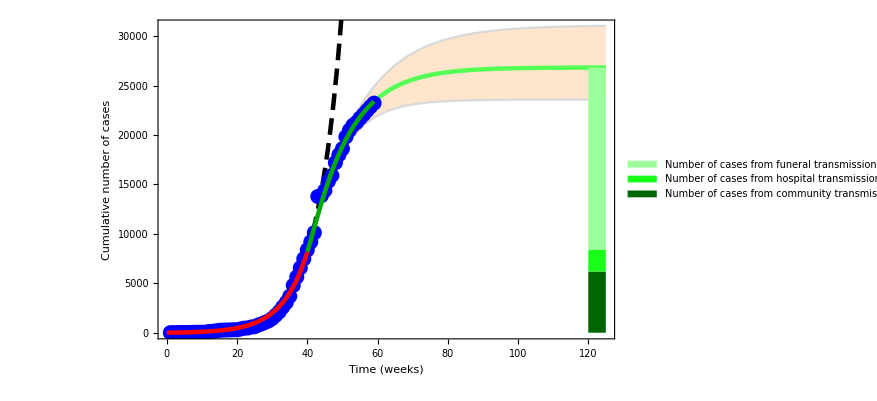

```mathematica
grextended2=Show[Plot[{-1,-1,-1},{x,0,125},Frame->True,PlotStyle->{Lighter[Red],Lighter[Blue],Orange},PlotRange->{0,31000},PlotLegends->SwatchLegend[Reverse[{Darker[Green,0.6],Lighter[Green,0.1],Lighter[Green,0.6]}],Reverse[{"Number of cases from community transmission","Number of cases from hospital transmission","Number of cases from funeral transmission"}]],FrameLabel->{Style["Time (weeks)",FontSize->20],Style["Cumulative number of cases",FontSize->20]},FrameStyle->Directive[FontSize->15],ImageSize->{650,400},FrameTicks->{{{0,5000,10000,15000,20000,25000,30000},None},{{0,10,20,30,40,50,60,70,80,90,100,110,120},None}}],
Plot[1000000(10^-7+alpha0 NIntegrate[Evaluate[samplesol[[sortedindices⟦1⟧]][[2]]/.{t->s}],{s,0,x}]),{x,0,70},PlotStyle->Directive[AbsoluteDashing[{12,6}],Black,Thickness[0.005]]],Plot[{1000000*upperbondcbai[x],1000000*lowerbondcbai[x]},{x,41,125},PlotStyle->{LightGray,LightGray},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Lighter[Orange,0.6]]],
ListPlot[Thread[{Range[Length[totalcasesweekly]],totalcasesweekly}],PlotStyle->Blue],Plot[1000000(E0+alpha0 NIntegrate[Evaluate[samplesolai[[sortedindicesai⟦1⟧]][[2]]/.{t->s}],{s,0,x}]),{x,0,40},PlotStyle->Directive[Red,Thickness[0.005]]],Plot[1000000(E0+alpha0 NIntegrate[Evaluate[samplesolai[[sortedindicesai⟦1⟧]][[2]]/.{t->s}],{s,0,x}]),{x,40,Length[totalcasesweekly]},PlotStyle->Directive[Darker[Green],Thickness[0.005]]],Plot[1000000(E0+alpha0 NIntegrate[Evaluate[samplesolai[[sortedindicesai⟦1⟧]][[2]]/.{t->s}],{s,0,x}]),{x,Length[totalcasesweekly],125},PlotStyle->Directive[Lighter[Green],Thickness[0.005]]],
Graphics[{Darker[Green,0.6],Polygon[{{120,0},{120,CommTrans},{125,CommTrans},{125,0}}],Lighter[Green,0.1],Polygon[{{120,CommTrans},{120,HospTrans+CommTrans},{125,HospTrans+CommTrans},{125,CommTrans}}],Lighter[Green,0.6],Polygon[{{120,HospTrans+CommTrans},{120,HospTrans+CommTrans+FunTrans},{125,HospTrans+CommTrans+FunTrans},{125,HospTrans+CommTrans}}]}]]
```

```mathematica
{{105,2.677*^4}}
```

{{105,26770.}}

```mathematica
Export["confidence_extended_2.eps",grextended2]
```

confidence_extended_2.eps

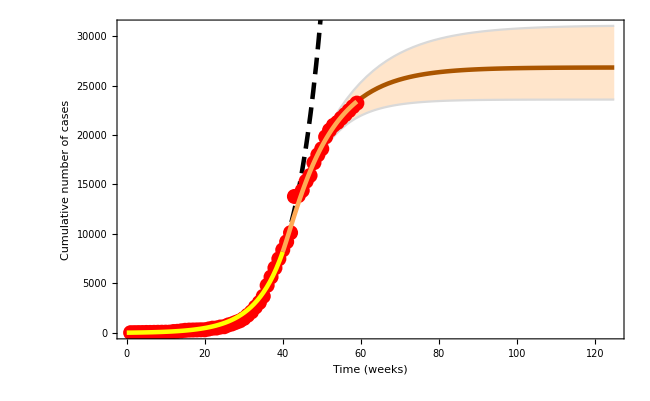

```mathematica
grextended2=Show[Plot[{-1,-1,-1},{x,0,125},Frame->True,PlotStyle->{Lighter[Red],Lighter[Blue],Orange},PlotRange->{0,31000},FrameLabel->{Style["Time (weeks)",FontSize->20],Style["Cumulative number of cases",FontSize->20]},FrameStyle->Directive[FontSize->15],ImageSize->{650,400},FrameTicks->{{{0,5000,10000,15000,20000,25000,30000},None},{{0,10,20,30,40,50,60,70,80,90,100,110,120},None}}],
Plot[1000000(10^-7+alpha0 NIntegrate[Evaluate[samplesol[[sortedindices⟦1⟧]][[2]]/.{t->s}],{s,0,x}]),{x,0,70},PlotStyle->Directive[AbsoluteDashing[{12,6}],Black,Thickness[0.005]]],Plot[{1000000*upperbondcbai[x],1000000*lowerbondcbai[x]},{x,41,125},PlotStyle->{LightGray,LightGray},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Lighter[Orange,0.6]]],
ListPlot[Thread[{Range[Length[totalcasesweekly]],totalcasesweekly}],PlotStyle->Red],Plot[1000000(E0+alpha0 NIntegrate[Evaluate[samplesolai[[sortedindicesai⟦1⟧]][[2]]/.{t->s}],{s,0,x}]),{x,0,40},PlotStyle->Directive[Yellow,Thickness[0.005]]],Plot[1000000(E0+alpha0 NIntegrate[Evaluate[samplesolai[[sortedindicesai⟦1⟧]][[2]]/.{t->s}],{s,0,x}]),{x,40,Length[totalcasesweekly]},PlotStyle->Directive[Lighter[Orange],Thickness[0.005]]],Plot[1000000(E0+alpha0 NIntegrate[Evaluate[samplesolai[[sortedindicesai⟦1⟧]][[2]]/.{t->s}],{s,0,x}]),{x,Length[totalcasesweekly],125},PlotStyle->Directive[Darker[Orange],Thickness[0.005]]]]
```

```mathematica
Export["confidence_extended_2.eps",grextended2]
```

confidence_extended_2.eps

### DATA - Final size after intervention (T=40)

```mathematica
samplefs=Transpose[ToExpression[Import["samplep5.xlsx"][[1]]]];
```

```mathematica
parameterfs={
{beta1,0.5*bbeta1,beta0},
{phi1,0.5*pphi1,phi0},
{theta1,0.5*ttheta1,theta0},
{b1,b0,2*bb1},
{eta1,eta0,2*eeta1}}
```

{{beta1,0.252723,0.531912},{phi1,0.557467,2.10387},{theta1,0.0477413,0.327954},{b1,1.30432,2.83422},{eta1,1.45437,3.37566}}

```mathematica
sampleparamfs=Table[Table[N[(parameterfs[[All,2;;3]][[j,2]]-parameterfs[[All,2;;3]][[j,1]])samplefs[[i,j]]+parameterfs[[All,2;;3]][[j,1]]],{j,1,Length[samplefs[[i]]]}],{i,1,Length[samplefs]}];
```

```mathematica
fsT40=Table[SSinf/.NSolve[((Log[SST]-Log[SSinf])/.{SST->ST})==(((1/(ST+ET+IT+RT)((φ/b u+y)/(u+x)(NNT-SSinf)-(φ/b u+y)/(u+x)RRT+φ/b DDT+HHT((φ/b u+y)/(u+x)(1-z/y+x/y v/u)-v/u)))/.{x->η(1-δH)γH+(γH+κ)(1-δ)γ,y->η θ+(γH+κ)β,z->(1-δH)γH β-(1-δ)γ θ,u->η δH γH+(γH+κ)δ γ,v->δH γH β-δ γ θ,NNT->SST+EET+RRT+IIT})/.
{β->sampleparamfs[[i,1]],
φ->sampleparamfs[[i,2]],
θ->sampleparamfs[[i,3]],
b->sampleparamfs[[i,4]],
η->sampleparamfs[[i,5]],
γ->gamma0,
δ->delta0,
γH->gammaT0,
δH->deltaT0,
κ->kappa0,
SST->ST,
EET->ET,
IIT->IT,
RRT->RT,
DDT->DT,
BBT->BT,
HHT->HT}),SSinf],{i,1,Length[sampleparamfs]}][[All,1]]//Quiet;
```

```mathematica
joint40=Join[{Join[parameterscbai[[All,1]][[1;;5]],{"Final_size"}]},Table[Join[sampleparamfs[[i]],{22-fsT40[[i]]}],{i,1,Length[sampleparamfs]}]];
```

```mathematica
goodones40=Join[{joint40[[1]]},Select[joint40[[2;;All]],(#[[6]]<0.1)&]];
```

```mathematica
Export["final_size_T40.csv",goodones40];
```

### PLOT - Asymptotic behavior without control

```mathematica
f=0.4
```

0.4

```mathematica
odewc[{W_?NumberQ,T_?NumberQ,β1_?NumberQ,φ1_?NumberQ,θ1_?NumberQ,b1_?NumberQ,η1_?NumberQ,qb_?NumericQ,qf_?NumericQ,qt_?NumericQ,qbb_?NumericQ,qe_?NumericQ,β0_?NumberQ,φ0_?NumberQ,θ0_?NumberQ,γ_?NumberQ,δ_?NumberQ,γT_?NumberQ,δT_?NumberQ,η0_?NumberQ,b0_?NumberQ,κ_?NumberQ,α_?NumberQ},{S0_?NumberQ,EE0_?NumberQ,II0_?NumberQ,RR0_?NumberQ,DD0_?NumberQ,BB0_?NumberQ,HH0_?NumberQ}]:=(odenewwc[{T,β1,φ1,θ1,b1,η1,qb,qf,qt,qbb,qe,β0,φ0,θ0,γ,δ,γT,δT,η0,b0,κ,α},{S0,EE0,II0,RR0,DD0,BB0,HH0}]=NDSolveValue[
{S'[t]==-1/22 Piecewise[{{β0,t<T},{β1+(β0-β1)Exp[-qb (t-T)],t≥T&&t≤W},{β0+f(β1-β0),t>W}}] S[t]II[t]
-1/22 Piecewise[{{φ0,t<T},{φ1+(φ0-φ1)Exp[-qf (t-T)],t≥T&&t≤W},{φ0+f(φ1-φ0),t>W}}]S[t]DD[t]
-1/22 Piecewise[{{θ0,t<T},{θ1+(θ0-θ1)Exp[-qt (t-T)],t≥T&&t≤W},{θ0+f(θ1-θ0),t>W}}] S[t]HH[t],
EE'[t]==1/22 Piecewise[{{β0,t<T},{β1+(β0-β1)Exp[-qb (t-T)],t≥T&&t≤W},{β0+f(β1-β0),t>W}}] S[t]II[t]
+1/22 Piecewise[{{φ0,t<T},{φ1+(φ0-φ1)Exp[-qf (t-T)],t≥T&&t≤W},{φ0+f(φ1-φ0),t>W}}] S[t]DD[t]
+1/22 Piecewise[{{θ0,t<T},{θ1+(θ0-θ1)Exp[-qt (t-T)],t≥T&&t≤W},{θ0+f(θ1-θ0),t>W}}] S[t]HH[t]
-α EE[t],
II'[t]==α EE[t]-γ II[t]-Piecewise[{{η0,t<T},{η1+(η0-η1)Exp[-qe (t-T)],t≥T&&t≤W},{η0+f(η1-η0),t>W}}] II[t]+κ II[t],
RR'[t]==(1-δ)γ II[t]+(1-δT)γT HH[t],
DD'[t]==δ γ II[t]-Piecewise[{{b0,t<T},{b1+(b0-b1)Exp[-qbb (t-T)],t≥T&&t≤W},{b0+f(b1-b0),t>W}}] DD[t]+δT γT HH[t],
BB'[t]==Piecewise[{{b0,t<T},{b1+(b0-b1)Exp[-qbb (t-T)],t≥T&&t≤W},{b0+f(b1-b0),t>W}}] DD[t],
HH'[t]==Piecewise[{{η0,t<T},{η1+(η0-η1)Exp[-qe (t-T)],t≥T&&t≤W},{η0+f(η1-η0),t>W}}] II[t]-γT HH[t]-κ HH[t],
S[0]==S0,EE[0]==EE0,II[0]==II0,RR[0]==RR0,DD[0]==DD0,BB[0]==BB0,HH[0]==HH0},{S[t],EE[t],II[t],RR[t],DD[t],BB[t],HH[t]},{t,0,250}])
```

```mathematica
W=120;
```

```mathematica
samplesolwc=odewc[Join[{W,T},sampleparamai[[sortedindicesai[[1]]]],{beta0,phi0,theta0,gamma0,delta0,gammaT0,deltaT0,eta0,b0,kappa0,alpha0}],{22,E0,I0,0,D0,0,H0}];
```

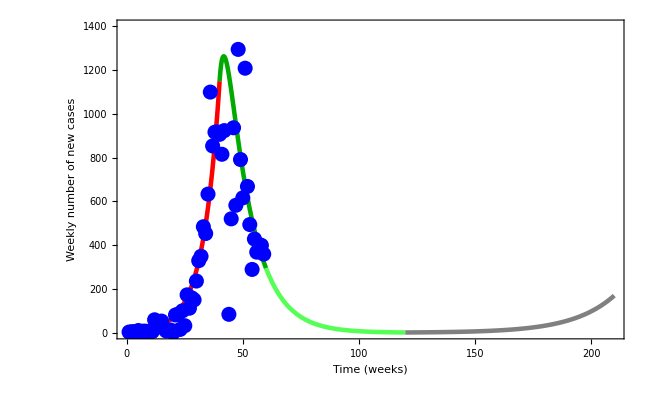

```mathematica
withoutcontrol=Show[Plot[-1,{t,0,210},Frame->True,PlotStyle->Directive[Red,Thickness[0.005]],PlotRange->{0,1400},FrameLabel->{Style["Time (weeks)",FontSize->20],Style["Weekly number of new cases",FontSize->20]},FrameTicks->{{{0,200,400,600,800,1000,1200,1400},None},{{0,50,100,150,200,250},None}},FrameStyle->Directive[FontSize->15],ImageSize->{650,400}],
Plot[1000000(Evaluate[alpha0 samplesolwc[[2]]]),{t,0,40},Frame->True,PlotStyle->Directive[Red,Thickness[0.005]]],
Plot[1000000(Evaluate[alpha0 samplesolwc[[2]]]),{t,40,60},PlotStyle->Directive[Darker[Green],Thickness[0.005]]],Plot[1000000(Evaluate[alpha0 samplesolwc[[2]]]),{t,60,120},PlotStyle->Directive[Lighter[Green],Thickness[0.005]]],
Plot[1000000(Evaluate[alpha0 samplesolwc[[2]]]),{t,120,210},PlotStyle->Directive[Gray,Thickness[0.005]]],ListPlot[Thread[{Range[Length[newinfectedweekly]],newinfectedweekly}],PlotStyle->Blue]]
```

```mathematica
Export["withoutcontrol.eps",withoutcontrol]
```

withoutcontrol.eps

### PLOT - Different final sizes - without q-s

Init

```mathematica
odeai2[{T_?NumberQ,β1_?NumberQ,φ1_?NumberQ,θ1_?NumberQ,b1_?NumberQ,η1_?NumberQ,β0_?NumberQ,φ0_?NumberQ,θ0_?NumberQ,γ_?NumberQ,δ_?NumberQ,γT_?NumberQ,δT_?NumberQ,η0_?NumberQ,b0_?NumberQ,κ_?NumberQ,α_?NumberQ},{S0_?NumberQ,EE0_?NumberQ,II0_?NumberQ,RR0_?NumberQ,DD0_?NumberQ,BB0_?NumberQ,HH0_?NumberQ}]:=(odenewai2[{T,β1,φ1,θ1,b1,η1,β0,φ0,θ0,γ,δ,γT,δT,η0,b0,κ,α},{S0,EE0,II0,RR0,DD0,BB0,HH0}]=NDSolveValue[
{S'[t]==-1/22 Piecewise[{{β0,t<T},{β1,t≥T}}] S[t]II[t]
-1/22 Piecewise[{{φ0,t<T},{φ1,t≥T}}]S[t]DD[t]
-1/22 Piecewise[{{θ0,t<T},{θ1,t≥T}}] S[t]HH[t],
EE'[t]==1/22 Piecewise[{{β0,t<T},{β1,t≥T}}] S[t]II[t]
+1/22 Piecewise[{{φ0,t<T},{φ1,t≥T}}] S[t]DD[t]
+1/22 Piecewise[{{θ0,t<T},{θ1,t≥T}}] S[t]HH[t]
-α EE[t],
II'[t]==α EE[t]-γ II[t]-Piecewise[{{η0,t<T},{η1,t≥T}}] II[t]+κ II[t],
RR'[t]==(1-δ)γ II[t]+(1-δT)γT HH[t],
DD'[t]==δ γ II[t]-Piecewise[{{b0,t<T},{b1,t≥T}}] DD[t]+δT γT HH[t],
BB'[t]==Piecewise[{{b0,t<T},{b1,t≥T}}] DD[t],
HH'[t]==Piecewise[{{η0,t<T},{η1,t≥T}}] II[t]-γT HH[t]-κ HH[t],
S[0]==S0,EE[0]==EE0,II[0]==II0,RR[0]==RR0,DD[0]==DD0,BB[0]==BB0,HH[0]==HH0},{S[t],EE[t],II[t],RR[t],DD[t],BB[t],HH[t]},{t,0,200}])
```

```mathematica
states2252=samplesol[[sortedindices[[1]]]]/.{t->25};
states2302=samplesol[[sortedindices[[1]]]]/.{t->30};
states2352=samplesol[[sortedindices[[1]]]]/.{t->35};
states2402=samplesol[[sortedindices[[1]]]]/.{t->40};
states2452=samplesol[[sortedindices[[1]]]]/.{t->45};
```

```mathematica
sampleparamai[[sortedindicesai[[1]]]][[1;;5]]
```

{0.505446,1.11493,0.0954826,1.41711,1.68783}

```mathematica
sol2252=odeai2[Join[{25},sampleparamai[[sortedindicesai[[1]]]][[1;;5]],{beta0,phi0,theta0,gamma0,delta0,gammaT0,deltaT0,eta0,b0,kappa0,alpha0}],{22,E0,I0,0,D0,0,H0}];
sol2302=odeai2[Join[{30},sampleparamai[[sortedindicesai[[1]]]][[1;;5]],{beta0,phi0,theta0,gamma0,delta0,gammaT0,deltaT0,eta0,b0,kappa0,alpha0}],{22,E0,I0,0,D0,0,H0}];
sol2352=odeai2[Join[{35},sampleparamai[[sortedindicesai[[1]]]][[1;;5]],{beta0,phi0,theta0,gamma0,delta0,gammaT0,deltaT0,eta0,b0,kappa0,alpha0}],{22,E0,I0,0,D0,0,H0}];
sol2402=odeai2[Join[{40},sampleparamai[[sortedindicesai[[1]]]][[1;;5]],{beta0,phi0,theta0,gamma0,delta0,gammaT0,deltaT0,eta0,b0,kappa0,alpha0}],{22,E0,I0,0,D0,0,H0}];
sol2452=odeai2[Join[{45},sampleparamai[[sortedindicesai[[1]]]][[1;;5]],{beta0,phi0,theta0,gamma0,delta0,gammaT0,deltaT0,eta0,b0,kappa0,alpha0}],{22,E0,I0,0,D0,0,H0}];
```

```mathematica
finalsize2252=22-(SSinf/.NSolve[((Log[SST]-Log[SSinf])/.{SST->states2252[[1]]})==((((1/(states2252[[1]]+states2252[[2]]+states2252[[4]]+states2252[[3]]))((φ/b u+y)/(u+x)(NNT-SSinf)-(φ/b u+y)/(u+x)RRT+φ/b DDT+HHT((φ/b u+y)/(u+x)(1-z/y+x/y v/u)-v/u)))/.{x->η(1-δH)γH+(γH+κ)(1-δ)γ,y->η θ+(γH+κ)β,z->(1-δH)γH β-(1-δ)γ θ,u->η δH γH+(γH+κ)δ γ,v->δH γH β-δ γ θ,NNT->SST+EET+RRT+IIT})/.
{β->sampleparamai[[sortedindicesai[[1]],1]],
φ->sampleparamai[[sortedindicesai[[1]],2]],
θ->sampleparamai[[sortedindicesai[[1]],3]],
b->sampleparamai[[sortedindicesai[[1]],4]],
η->sampleparamai[[sortedindicesai[[1]],5]],
γ->sampleparam[[sortedindices[[1]]]][[4]],
δ->sampleparam[[sortedindices[[1]]]][[5]],
γH->sampleparam[[sortedindices[[1]]]][[6]],
δH->sampleparam[[sortedindices[[1]]]][[7]],
κ->sampleparam[[sortedindices[[1]]]][[10]],
SST->states2252[[1]],
EET->states2252[[2]],
IIT->states2252[[3]],
RRT->states2252[[4]],
DDT->states2252[[5]],
BBT->states2252[[6]],
HHT->states2252[[7]]}),SSinf][[1]])//Quiet;
```

```mathematica
finalsize2302=22-(SSinf/.NSolve[((Log[SST]-Log[SSinf])/.{SST->states2302[[1]]})==((((1/(states2302[[1]]+states2302[[2]]+states2302[[4]]+states2302[[3]]))((φ/b u+y)/(u+x)(NNT-SSinf)-(φ/b u+y)/(u+x)RRT+φ/b DDT+HHT((φ/b u+y)/(u+x)(1-z/y+x/y v/u)-v/u)))/.{x->η(1-δH)γH+(γH+κ)(1-δ)γ,y->η θ+(γH+κ)β,z->(1-δH)γH β-(1-δ)γ θ,u->η δH γH+(γH+κ)δ γ,v->δH γH β-δ γ θ,NNT->SST+EET+RRT+IIT})/.
{β->sampleparamai[[sortedindicesai[[1]],1]],
φ->sampleparamai[[sortedindicesai[[1]],2]],
θ->sampleparamai[[sortedindicesai[[1]],3]],
b->sampleparamai[[sortedindicesai[[1]],4]],
η->sampleparamai[[sortedindicesai[[1]],5]],
γ->sampleparam[[sortedindices[[1]]]][[4]],
δ->sampleparam[[sortedindices[[1]]]][[5]],
γH->sampleparam[[sortedindices[[1]]]][[6]],
δH->sampleparam[[sortedindices[[1]]]][[7]],
κ->sampleparam[[sortedindices[[1]]]][[10]],
SST->states2302[[1]],
EET->states2302[[2]],
IIT->states2302[[3]],
RRT->states2302[[4]],
DDT->states2302[[5]],
BBT->states2302[[6]],
HHT->states2302[[7]]}),SSinf][[1]])//Quiet;
```

```mathematica
finalsize2352=22-(SSinf/.NSolve[((Log[SST]-Log[SSinf])/.{SST->states2352[[1]]})==((((1/(states2352[[1]]+states2352[[2]]+states2352[[4]]+states2352[[3]]))((φ/b u+y)/(u+x)(NNT-SSinf)-(φ/b u+y)/(u+x)RRT+φ/b DDT+HHT((φ/b u+y)/(u+x)(1-z/y+x/y v/u)-v/u)))/.{x->η(1-δH)γH+(γH+κ)(1-δ)γ,y->η θ+(γH+κ)β,z->(1-δH)γH β-(1-δ)γ θ,u->η δH γH+(γH+κ)δ γ,v->δH γH β-δ γ θ,NNT->SST+EET+RRT+IIT})/.
{β->sampleparamai[[sortedindicesai[[1]],1]],
φ->sampleparamai[[sortedindicesai[[1]],2]],
θ->sampleparamai[[sortedindicesai[[1]],3]],
b->sampleparamai[[sortedindicesai[[1]],4]],
η->sampleparamai[[sortedindicesai[[1]],5]],
γ->sampleparam[[sortedindices[[1]]]][[4]],
δ->sampleparam[[sortedindices[[1]]]][[5]],
γH->sampleparam[[sortedindices[[1]]]][[6]],
δH->sampleparam[[sortedindices[[1]]]][[7]],
κ->sampleparam[[sortedindices[[1]]]][[10]],
SST->states2352[[1]],
EET->states2352[[2]],
IIT->states2352[[3]],
RRT->states2352[[4]],
DDT->states2352[[5]],
BBT->states2352[[6]],
HHT->states2352[[7]]}),SSinf][[1]])//Quiet;
```

```mathematica
finalsize2402=22-(SSinf/.NSolve[((Log[SST]-Log[SSinf])/.{SST->states2402[[1]]})==((((1/(states2402[[1]]+states2402[[2]]+states2402[[4]]+states2402[[3]]))((φ/b u+y)/(u+x)(NNT-SSinf)-(φ/b u+y)/(u+x)RRT+φ/b DDT+HHT((φ/b u+y)/(u+x)(1-z/y+x/y v/u)-v/u)))/.{x->η(1-δH)γH+(γH+κ)(1-δ)γ,y->η θ+(γH+κ)β,z->(1-δH)γH β-(1-δ)γ θ,u->η δH γH+(γH+κ)δ γ,v->δH γH β-δ γ θ,NNT->SST+EET+RRT+IIT})/.
{β->sampleparamai[[sortedindicesai[[1]],1]],
φ->sampleparamai[[sortedindicesai[[1]],2]],
θ->sampleparamai[[sortedindicesai[[1]],3]],
b->sampleparamai[[sortedindicesai[[1]],4]],
η->sampleparamai[[sortedindicesai[[1]],5]],
γ->sampleparam[[sortedindices[[1]]]][[4]],
δ->sampleparam[[sortedindices[[1]]]][[5]],
γH->sampleparam[[sortedindices[[1]]]][[6]],
δH->sampleparam[[sortedindices[[1]]]][[7]],
κ->sampleparam[[sortedindices[[1]]]][[10]],
SST->states2402[[1]],
EET->states2402[[2]],
IIT->states2402[[3]],
RRT->states2402[[4]],
DDT->states2402[[5]],
BBT->states2402[[6]],
HHT->states2402[[7]]}),SSinf][[1]])//Quiet;
```

```mathematica
finalsize2452=22-(SSinf/.NSolve[((Log[SST]-Log[SSinf])/.{SST->states2452[[1]]})==((((1/(states2452[[1]]+states2452[[2]]+states2452[[4]]+states2452[[3]]))((φ/b u+y)/(u+x)(NNT-SSinf)-(φ/b u+y)/(u+x)RRT+φ/b DDT+HHT((φ/b u+y)/(u+x)(1-z/y+x/y v/u)-v/u)))/.{x->η(1-δH)γH+(γH+κ)(1-δ)γ,y->η θ+(γH+κ)β,z->(1-δH)γH β-(1-δ)γ θ,u->η δH γH+(γH+κ)δ γ,v->δH γH β-δ γ θ,NNT->SST+EET+RRT+IIT})/.
{β->sampleparamai[[sortedindicesai[[1]],1]],
φ->sampleparamai[[sortedindicesai[[1]],2]],
θ->sampleparamai[[sortedindicesai[[1]],3]],
b->sampleparamai[[sortedindicesai[[1]],4]],
η->sampleparamai[[sortedindicesai[[1]],5]],
γ->sampleparam[[sortedindices[[1]]]][[4]],
δ->sampleparam[[sortedindices[[1]]]][[5]],
γH->sampleparam[[sortedindices[[1]]]][[6]],
δH->sampleparam[[sortedindices[[1]]]][[7]],
κ->sampleparam[[sortedindices[[1]]]][[10]],
SST->states2452[[1]],
EET->states2452[[2]],
IIT->states2452[[3]],
RRT->states2452[[4]],
DDT->states2452[[5]],
BBT->states2452[[6]],
HHT->states2452[[7]]}),SSinf][[1]])//Quiet;
```

```mathematica
{finalsize2252,finalsize2302,finalsize2352,finalsize2402,finalsize2452}
```

{0.00236523,0.00479516,0.00968309,0.019508,0.0392268}

```mathematica
table[pairs_]:=TableForm[pairs,TableAlignments->Center]
```

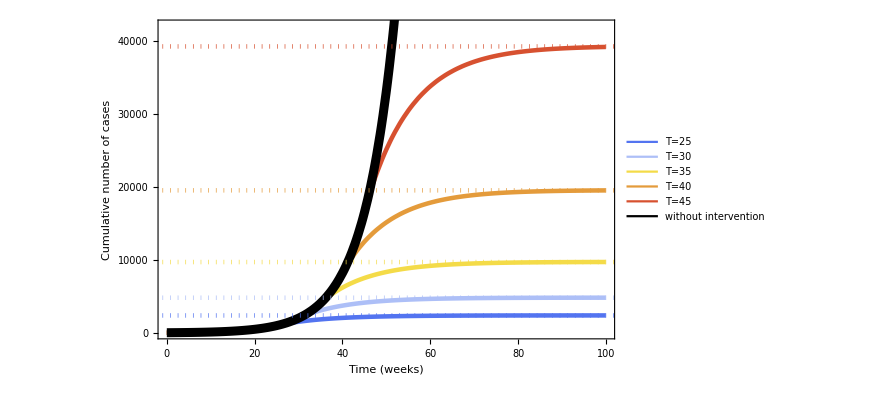

```mathematica
difffs2=Show[Plot[{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{x,0,100},Frame->True,FrameLabel->{Style["Time (weeks)",FontSize->20],Style["Cumulative number of cases",FontSize->20]},FrameStyle->Directive[FontSize->15],
PlotStyle->{
RGBColor[{0.32547626067139757,0.45633291090621336,0.9419600374159929}],
RGBColor[{0.6772114934352562,0.747762032760383,0.9684617708305574}],
RGBColor[{0.9550175586546577,0.8593666401153697,0.28266427570117697}],RGBColor[{0.8928899682625857,0.6065201867114359,0.23233710282222436}],RGBColor[{0.8411931874816556,0.31763446671966794,0.18707994889447163}],
Black,
Directive[RGBColor[{0.32547626067139757,0.45633291090621336,0.9419600374159929}],Dashed],
Directive[RGBColor[{0.6772114934352562,0.747762032760383,0.9684617708305574}],Dashed],
Directive[RGBColor[{0.9550175586546577,0.8593666401153697,0.28266427570117697}],Dashed],
Directive[RGBColor[{0.8928899682625857,0.6065201867114359,0.23233710282222436}],Dashed],Directive[RGBColor[{0.8411931874816556,0.31763446671966794,0.18707994889447163}],Dashed]},PlotRange->{0,42000},ImageSize->{650,400},FrameTicks->{{{0,10000,20000,30000,40000},None},{{0,20,40,60,80,100,120,140,160},None}},
PlotLegends->LineLegend[{RGBColor[{0.32547626067139757,0.45633291090621336,0.9419600374159929}],
RGBColor[{0.6772114934352562,0.747762032760383,0.9684617708305574}],
RGBColor[{0.9550175586546577,0.8593666401153697,0.28266427570117697}],RGBColor[{0.8928899682625857,0.6065201867114359,0.23233710282222436}],RGBColor[{0.8411931874816556,0.31763446671966794,0.18707994889447163}],
Black},{"T=25","T=30","T=35","T=40","T=45","without intervention"},LegendMarkerSize->{20,5},LegendFunction->Framed,LegendLayout->table]],
Show[Plot[1000000(10^-7+alpha0 NIntegrate[Evaluate[sol2252[[2]]/.{t->s}],{s,0,x}]),{x,0,100},
PlotStyle->Directive[RGBColor[{0.32547626067139757,0.45633291090621336,0.9419600374159929}],Thickness[0.005]]],Plot[1000000(10^-7+alpha0 NIntegrate[Evaluate[sol2302[[2]]/.{t->s}],{s,0,x}]),{x,0,100},PlotStyle->Directive[RGBColor[{0.6772114934352562,0.747762032760383,0.9684617708305574}],Thickness[0.005]]],
Plot[1000000(10^-7+alpha0 NIntegrate[Evaluate[sol2352[[2]]/.{t->s}],{s,0,x}]),{x,0,100},PlotStyle->Directive[RGBColor[{0.9550175586546577,0.8593666401153697,0.28266427570117697}],Thickness[0.005]]],
Plot[1000000(10^-7+alpha0 NIntegrate[Evaluate[sol2402[[2]]/.{t->s}],{s,0,x}]),{x,0,100},PlotStyle->Directive[RGBColor[{0.8928899682625857,0.6065201867114359,0.23233710282222436}],Thickness[0.005]]],
Plot[1000000(10^-7+alpha0 NIntegrate[Evaluate[sol2452[[2]]/.{t->s}],{s,0,x}]),{x,0,100},PlotStyle->Directive[RGBColor[{0.8411931874816556,0.31763446671966794,0.18707994889447163}],Thickness[0.005]]],Plot[1000000(10^-7+alpha0 NIntegrate[Evaluate[samplesol[[sortedindices⟦1⟧]][[2]]/.{t->s}],{s,0,x}]),{x,0,70},PlotStyle->Directive[Black,Thickness[0.01]]]],
Plot[{1000000finalsize2252,1000000finalsize2302,1000000finalsize2352,1000000finalsize2402,1000000finalsize2452},{x,-1,160},PlotStyle->{
Directive[RGBColor[{0.32547626067139757,0.45633291090621336,0.9419600374159929}],Dotted,Thickness[0.005]],
Directive[RGBColor[{0.6772114934352562,0.747762032760383,0.9684617708305574}],Dotted,Thickness[0.005]],
Directive[RGBColor[{0.9550175586546577,0.8593666401153697,0.28266427570117697}],Dotted,Thickness[0.005]],
Directive[RGBColor[{0.8928899682625857,0.6065201867114359,0.23233710282222436}],Dotted,Thickness[0.005]],Directive[RGBColor[{0.8411931874816556,0.31763446671966794,0.18707994889447163}],Dotted,Thickness[0.005]]}]]
```

```mathematica
Export["different_final_sizes_2.eps",difffs2]
```

different_final_sizes_2.eps

### PLOT - Tornado plots

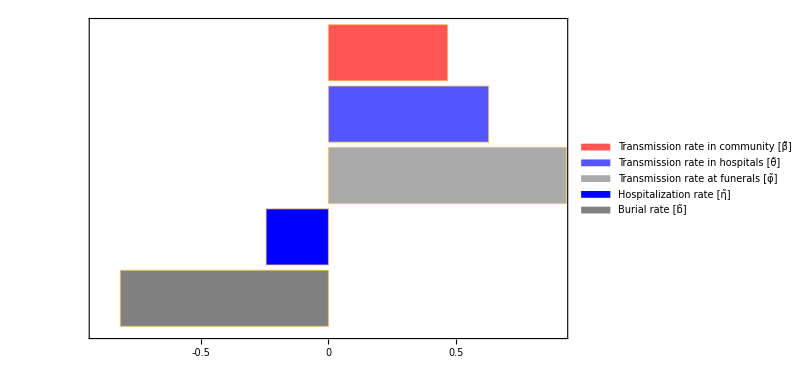

```mathematica
tornadofs=BarChart[Reverse[{0.4662126,0.6265938,0.9305566,-0.2438454,-0.8143913}],Frame->True,BarOrigin->Left,ChartLegends->SwatchLegend[Reverse[{"Transmission rate in community [β̃]","Transmission rate in hospitals [θ̃]","Transmission rate at funerals [φ̃]","Hospitalization rate [η̃]","Burial rate [b̃]"}],LabelStyle->20,LegendMarkerSize->15,LegendFunction->"Frame"],ChartStyle->Reverse[{Lighter[Red],Lighter[Blue],Lighter[Gray],Blue,Gray}],FrameTicks->{{None,None},{{-1,-0.5,0,0.5,1},None}},PlotRange->{-0.9,0.9},ImageSize->{600,400},FrameTicksStyle->Directive[Black,20]]
```

```mathematica
Export["tornadofs.eps",tornadofs]
```

tornadofs.eps

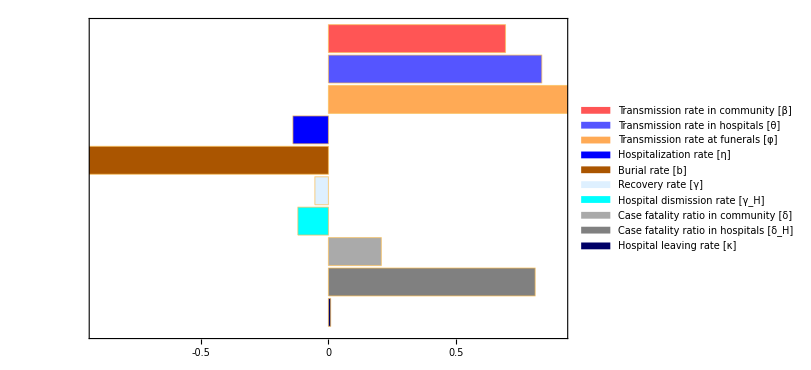

```mathematica
tornadoR0=BarChart[Reverse[{0.692597952,0.834619168,0.987454169,-0.139077051,-0.951814897,-0.053190568,-0.119662450,0.206907828,0.808793961,0.008629178}],Frame->True,BarOrigin->Left,ChartLegends->SwatchLegend[Reverse[{"Transmission rate in community [β]","Transmission rate in hospitals [θ]","Transmission rate at funerals [φ]","Hospitalization rate [η]","Burial rate [b]","Recovery rate [γ]","Hospital dismission rate [γ_H]","Case fatality ratio in community [δ]","Case fatality ratio in hospitals [δ_H]","Hospital leaving rate [κ]"}],LabelStyle->20,LegendMarkerSize->15,LegendFunction->"Frame"],ChartStyle->Reverse[{Lighter[Red],Lighter[Blue],Lighter[Orange],Blue,Darker[Orange],LightBlue,Cyan,Lighter[Gray],Gray,Darker[Blue,.6]}],FrameTicks->{{None,None},{{-1,-0.5,0,0.5,1},None}},PlotRange->{-0.9,0.9},ImageSize->{600,400},FrameTicksStyle->Directive[Black,20]]
```

```mathematica
Export["tornadoR0.eps",tornadoR0]
```

tornadoR0.eps

### DATA - Final Size Relation for ContourPlot

```mathematica
((Log[SST]-Log[SSinf])/.{SST->ST})//FullSimplify
```

3.0906-Log[SSinf]

φ-θ

```mathematica
(((1/(ST+ET+IT+RT)((φ/b u+y)/(u+x)(NNT-SSinf)-(φ/b u+y)/(u+x)RRT+φ/b DDT+HHT((φ/b u+y)/(u+x)(1-z/y+x/y v/u)-v/u)))/.{x->η(1-δH)γH+(γH+κ)(1-δ)γ,y->η θ+(γH+κ)β,z->(1-δH)γH β-(1-δ)γ θ,u->η δH γH+(γH+κ)δ γ,v->δH γH β-δ γ θ,NNT->SST+EET+RRT+IIT})/.
{β->bbeta1,
b->bb1,
η->eeta1,
γ->gamma0,
δ->delta0,
γH->gammaT0,
δH->deltaT0,
κ->kappa0,
SST->ST,
EET->ET,
IIT->IT,
RRT->RT,
DDT->DT,
BBT->BT,
HHT->HT})//FullSimplify
```

0.214525+0.467358 θ+SSinf (-0.00975451-0.0212503 θ-0.0207438 φ)+0.456228 φ

b-φ

```mathematica
(((1/(ST+ET+IT+RT)((φ/b u+y)/(u+x)(NNT-SSinf)-(φ/b u+y)/(u+x)RRT+φ/b DDT+HHT((φ/b u+y)/(u+x)(1-z/y+x/y v/u)-v/u)))/.{x->η(1-δH)γH+(γH+κ)(1-δ)γ,y->η θ+(γH+κ)β,z->(1-δH)γH β-(1-δ)γ θ,u->η δH γH+(γH+κ)δ γ,v->δH γH β-δ γ θ,NNT->SST+EET+RRT+IIT})/.
{β->bbeta1,
θ->ttheta1,
η->eeta1,
γ->gamma0,
δ->delta0,
γH->gammaT0,
δH->deltaT0,
κ->kappa0,
SST->ST,
EET->ET,
IIT->IT,
RRT->RT,
DDT->DT,
BBT->BT,
HHT->HT})//FullSimplify
```

(0.259149 b-0.0117835 b SSinf+0.646526 φ-0.0293963 SSinf φ)/b

b-θ

```mathematica
(((1/(ST+ET+IT+RT)((φ/b u+y)/(u+x)(NNT-SSinf)-(φ/b u+y)/(u+x)RRT+φ/b DDT+HHT((φ/b u+y)/(u+x)(1-z/y+x/y v/u)-v/u)))/.{x->η(1-δH)γH+(γH+κ)(1-δ)γ,y->η θ+(γH+κ)β,z->(1-δH)γH β-(1-δ)γ θ,u->η δH γH+(γH+κ)δ γ,v->δH γH β-δ γ θ,NNT->SST+EET+RRT+IIT})/.
{β->bbeta1,
φ->pphi1,
η->eeta1,
γ->gamma0,
δ->delta0,
γH->gammaT0,
δH->deltaT0,
κ->kappa0,
SST->ST,
EET->ET,
IIT->IT,
RRT->RT,
DDT->DT,
BBT->BT,
HHT->HT})//FullSimplify
```

(0.720834-0.0327749 SSinf+b (0.214525+SSinf (-0.00975451-0.0212503 θ)+0.467358 θ))/b

### PLOT - ContourPlots

#### φ-θ

```mathematica
data=Quiet[Flatten[Table[{{φ,θ},22-SSinf}/.(NSolve[3.0905965348976965-Log[SSinf]==0.2145245600015818+0.46735777649028776 θ+SSinf (-0.00975450894538428-0.02125033253242391 θ-0.020743790928838587 φ)+0.4562280238247687 φ,SSinf,Reals][[1]]),{φ,0,2.5,0.01},{θ,0.,0.25,0.01}],1]];
```

```mathematica
data[[1]]
```

{{0.,0.},0.0103969}

```mathematica
func=Interpolation[data]
```

InterpolatingFunction[{{0., 2.5}, {0., 0.25}}, <>]

```mathematica
func[0,0]
```

0.0103969

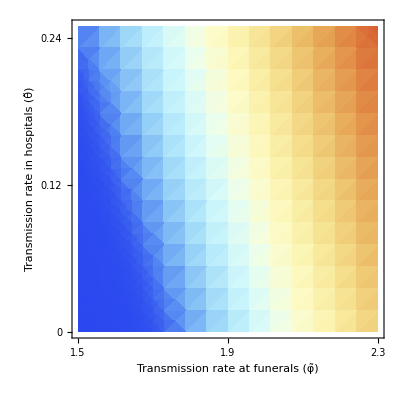

```mathematica
phitheta=Show[DensityPlot[func[φ,θ],{φ,1.5,2.3},{θ,0.,0.25},PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRangePadding->0],FrameTicks->{{{0,0.12,0.24},None},{{1.5,1.9,2.3},None}},FrameStyle->Directive[Black,FontSize->15,FontFamily->"Times New Roman"],FrameLabel->{Style["Transmission rate at funerals (φ̃)", FontSize->20],Style["Transmission rate in hospitals (θ̃)", FontSize->20]}]
```

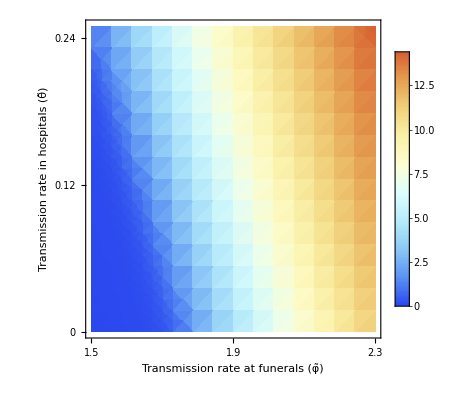

```mathematica
phitheta2=Show[DensityPlot[func[φ,θ],{φ,1.5,2.3},{θ,0.,0.25},PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRangePadding->0,PlotLegends->BarLegend[{"LightTemperatureMap",{0.1,14.4}},LegendMarkerSize->{25,300}]],FrameTicks->{{{0,0.12,0.24},None},{{1.5,1.9,2.3},None}},FrameStyle->Directive[Black,FontSize->15,FontFamily->"Times New Roman"],FrameLabel->{Style["Transmission rate at funerals (φ̃)", FontSize->20],Style["Transmission rate in hospitals (θ̃)", FontSize->20]}]
```

```mathematica
Export["contours_phi_theta.eps",phitheta]
```

contours_phi_theta.eps

```mathematica
Export["contours_phi_theta_2.eps",phitheta2]
```

contours_phi_theta_2.eps

#### b-θ

```mathematica
data2=Quiet[Flatten[Table[{{b,θ},22-SSinf}/.(NSolve[3.0905965348976965-Log[SSinf]==b/7(0.7208341401944237-0.0327749106098433 SSinf+7/b (0.21452456000158182+SSinf (-0.009754508945384282-0.02125033253242391 θ)+0.46735777649028776 θ)),SSinf,Reals][[1]]),{b,7/1,7/0.5,7/50},{θ,0.,0.25,0.01}],1]];
```

```mathematica
data2[[1]]
```

{{7,0.},0.0528188}

```mathematica
Max[data2[[All,2]]]
```

15.8875

```mathematica
func2=Interpolation[data2]
```

InterpolatingFunction[{{7., 14.}, {0., 0.25}}, <>]

```mathematica
func2[14,0]
```

14.7602

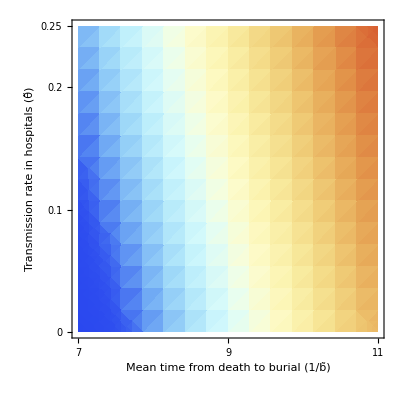

```mathematica
btheta=Show[DensityPlot[func2[b,θ],{b,7,11.},{θ,0.,0.25},PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRangePadding->0],FrameTicks->{{{0,0.1,0.2,0.25},None},{{7,9,11},None}},FrameStyle->Directive[Black,FontSize->15,FontFamily->"Times New Roman"],FrameLabel->{Style["Mean time from death to burial (1/b̃)", FontSize->20],Style["Transmission rate in hospitals (θ̃)", FontSize->20]}]
```

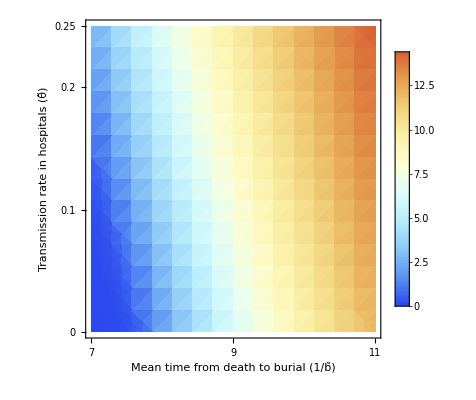

```mathematica
btheta2=Show[DensityPlot[func2[b,θ],{b,7,11.},{θ,0.,0.25},PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRangePadding->0,PlotLegends->BarLegend[{"LightTemperatureMap",{0.1,14.4}},LegendMarkerSize->{25,300}]],FrameTicks->{{{0,0.1,0.2,0.25},None},{{7,9,11},None}},FrameStyle->Directive[Black,FontSize->15,FontFamily->"Times New Roman"],FrameLabel->{Style["Mean time from death to burial (1/b̃)", FontSize->20],Style["Transmission rate in hospitals (θ̃)", FontSize->20]}]
```

```mathematica
Export["contours_b_theta.eps",btheta]
```

contours_b_theta.eps

```mathematica
Export["contours_b_theta_2.eps",btheta2]
```

contours_b_theta_2.eps

#### b-φ

```mathematica
data3=Quiet[Flatten[Table[{{b,φ},22-SSinf}/.(NSolve[3.0905965348976965-Log[SSinf]==(0.2591490835523929 7/b-0.01178354539723719 7/b SSinf+0.6465257552217345 φ-0.02939625449571305 SSinf φ)/(7/b),SSinf,Reals][[1]]),{b,7/0.8,7/0.5,5.25/30},{φ,0.6,1.2,0.01}],1]];
```

```mathematica
data3[[1]]
```

{{8.75,0.6},0.018305}

```mathematica
Max[data3[[All,2]]]
```

16.2059

```mathematica
func3=Interpolation[data3]
```

InterpolatingFunction[{{8.75, 14.}, {0.6, 1.2}}, <>]

```mathematica
func3[0.01,0]
```

InterpolatingFunction::dmval: Input value {0.01, 0} lies outside the range of data in the interpolating function. Extrapolation will be used.

40.3432

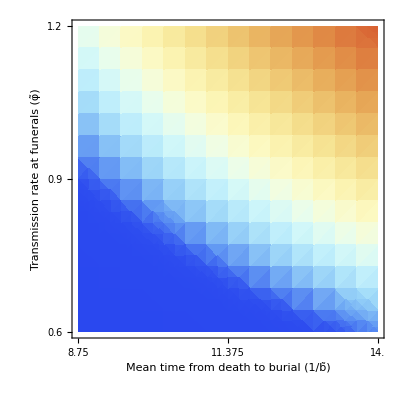

```mathematica
bphi=Show[DensityPlot[func3[b,φ],{b,7/0.8,7/0.5},{φ,0.6,1.2},PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRangePadding->0],FrameStyle->Directive[Black,FontSize->15,FontFamily->"Times New Roman"],FrameTicks->{{{0.6,0.9,1.2},None},{{7/0.8,(7/0.8+7/0.5)/2,7/0.5},None}},FrameLabel->{Style["Mean time from death to burial (1/b̃)", FontSize->20],Style["Transmission rate at funerals (φ̃)", FontSize->20]}]
```

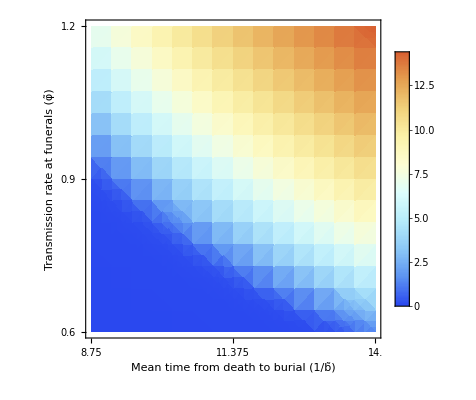

```mathematica
bphi2=Show[DensityPlot[func3[b,φ],{b,7/0.8,7/0.5},{φ,0.6,1.2},PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRangePadding->0,PlotLegends->BarLegend[{"LightTemperatureMap",{0.1,14.4}},LegendMarkerSize->{25,300}]],FrameTicks->{{{0.6,0.9,1.2},None},{{7/0.8,(7/0.8+7/0.5)/2,7/0.5},None}},FrameStyle->Directive[Black,FontSize->15,FontFamily->"Times New Roman"],FrameLabel->{Style["Mean time from death to burial (1/b̃)", FontSize->20],Style["Transmission rate at funerals (φ̃)", FontSize->20]}]
```

```mathematica
Export["contours_b_phi.eps",bphi]
```

contours_b_phi.eps

```mathematica
Export["contours_b_phi_2.eps",bphi2]
```

contours_b_phi_2.eps

#### Multifigure

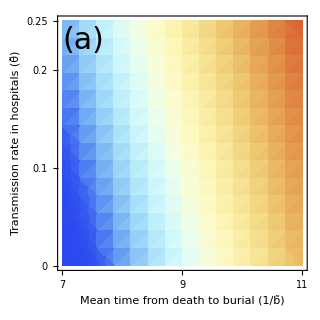
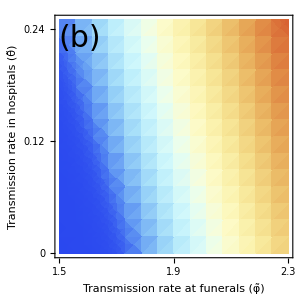
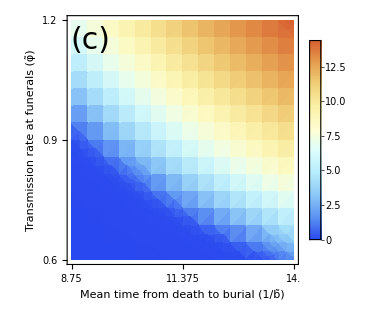
-Graphics-    -Graphics-
-Graphics--Graphics-

```mathematica
multicontour=Column[{Row[{Show[DensityPlot[func2[b,θ],{b,7,11.},{θ,0.,0.25},PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRangePadding->0,ImageSize->{320,320}],Graphics[{Text[Style["(a)",FontSize->30],{7.35,0.23}]}],FrameTicks->{{{0,0.1,0.2,0.25},None},{{7,9,11},None}},FrameStyle->Directive[Black,FontSize->15,FontFamily->"Times New Roman"],FrameLabel->{Style["Mean time from death to burial (1/b̃)", FontSize->20],Style["Transmission rate in hospitals (θ̃)", FontSize->20]}],"    ",Show[DensityPlot[func[φ,θ],{φ,1.5,2.3},{θ,0.,0.25},PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRangePadding->0,ImageSize->{305,305}],Graphics[{Text[Style["(b)",FontSize->30],{1.57,0.23}]}],FrameTicks->{{{0,0.12,0.24},None},{{1.5,1.9,2.3},None}},FrameStyle->Directive[Black,FontSize->15,FontFamily->"Times New Roman"],FrameLabel->{Style["Transmission rate at funerals (φ̃)", FontSize->20],Style["Transmission rate in hospitals (θ̃)", FontSize->20]}]}],Row[{Show[DensityPlot[func3[b,φ],{b,7/0.8,7/0.5},{φ,0.6,1.2},PlotRange->All,ColorFunction->"LightTemperatureMap",PlotRangePadding->0,PlotLegends->BarLegend[{"LightTemperatureMap",{0.1,14.4}},LegendMarkerSize->{25,300}],ImageSize->{320,320}],Graphics[{Text[Style["(c)",FontSize->30],{7/0.8+0.45,1.15}]}],FrameTicks->{{{0.6,0.9,1.2},None},{{7/0.8,(7/0.8+7/0.5)/2,7/0.5},None}},FrameStyle->Directive[Black,FontSize->15,FontFamily->"Times New Roman"],FrameLabel->{Style["Mean time from death to burial (1/b̃)", FontSize->20],Style["Transmission rate at funerals (φ̃)", FontSize->20]},ImageSize->{313,313}],Show[Graphics[{White,Point[{0,0}]}]]}]}]
```

```mathematica
Export["multicontour_fig_6.eps",multicontour]
```

multicontour_fig_6.eps